```mathematica
path = FileNameJoin[Drop[#,Flatten@{Position[#,"Master"]+1,-1}]&@StringSplit[NotebookDirectory[],"\\"]];
```

```mathematica
ClearAll[data11]
data11=Table[Import[path<>"\\Data\\2017\\may\\11\\may11_"<>ToString[i]<>".dat"],{i,6,9}];
```

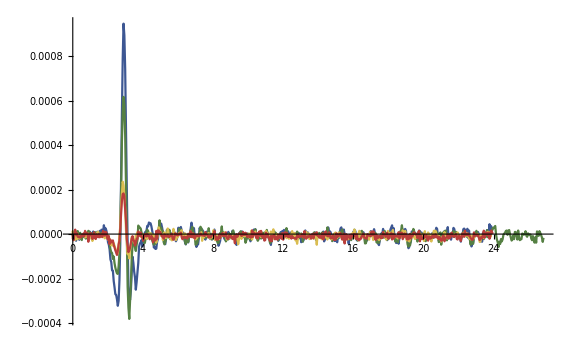

```mathematica
ListLinePlot[Table[data11[[i,All,{3,2}]],{i,1,4}],PlotRange->All,ImageSize->Large,PlotStyle->"DarkRainbow"]
```

```mathematica
fourier = Table[Fourier[data11[[i,All,2]][[;;512]]],{i,1,4}];
```

```mathematica
frequency = Range[512]/data11[[1,512,3]];
```

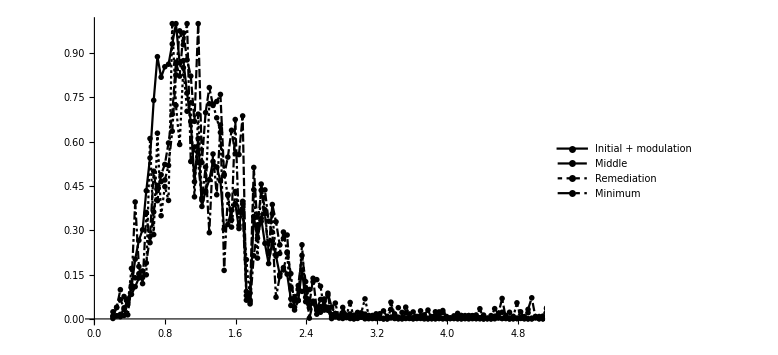

```mathematica
ListLinePlot[Table[Transpose[{frequency[[5;;]],Abs[fourier[[i]][[5;;512]]]^2/(Max[Abs[fourier[[i]][[5;;512]]]^2])}],{i,4}],PlotRange->{{0,5},All},ImageSize->Large,PlotTheme->"Monochrome",PlotLegends->{"Initial + modulation","Middle","Remediation","Minimum"}]
```